```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/LISA_Fisher/math

## ρ*

```mathematica
Mpl=2.435 10^18;
c=299792458;
Mpcinm=3.086 10^16 10^6;
GeVinminv=10^9/(1.973 10^-7);
GeVinMpcinv=GeVinminv Mpcinm;
MpcinvinHz=c/Mpcinm;
```

```mathematica
w[ρ_]=1/3-σ/(ρ/ρs)Sqrt[π/2] E^(σ^2/2)(1/3-cs2min)Erfc[(σ^2-Log[ρ/ρs])/(Sqrt[2]σ)];
```

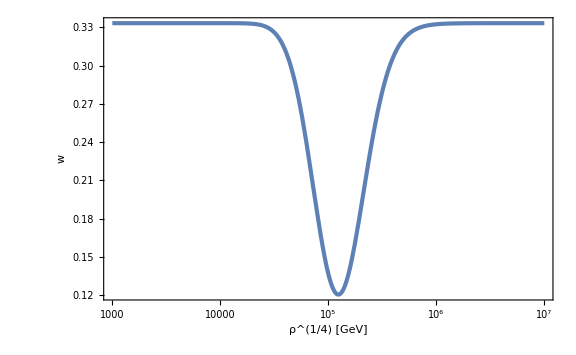

```mathematica
LogLinearPlot[w[ρquar^4]/.{ρs->10^(5 4),cs2min->0.1,σ->2},{ρquar,10^3,10^7},FrameLabel->{"ρ^(1/4) [GeV]",w}]
```

```mathematica
a1e4=1.927 10^-17;
η1e4=1.4 10^-11;
ηi=0;
```

```mathematica
bgsol=NDSolve[{ρ'[η]/GeVinMpcinv==(-Sqrt[3])/Mpl(1+w[ρ[η]])a[η] ρ[η]^(3/2),a'[η]/GeVinMpcinv==Sqrt[ρ[η]/3] a[η]^2/Mpl,a[η1e4]==a1e4,ρ[η1e4]==10^(4 4)}/.{ρs->10^(5 4),cs2min->0.1,σ->2},{ρ[η],a[η]},{η,ηi,η1e4}][[1]];
```

```mathematica
asol[η_]=a[η]/.bgsol;
ρsol[η_]=ρ[η]/.bgsol;
ℋsol[η_]=Sqrt[ρsol[η]]/(Sqrt[3]Mpl)asol[η]GeVinMpcinv;
```

```mathematica
asol[η1e4]
```

1.927×10^-17

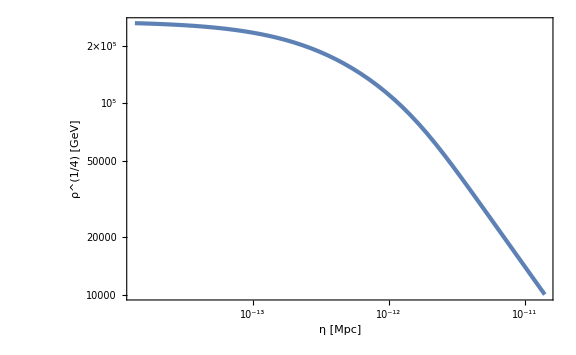

```mathematica
LogLogPlot[ρsol[η]^(1/4),{η,ηi,η1e4},FrameLabel->{"η [Mpc]","ρ^(1/4) [GeV]"},PlotRange->Full]
```

```mathematica
ks=ℋsol[η]/.FindRoot[ρsol[η]==10^(5 4),{η,10^-12},WorkingPrecision->30]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

6.59363×10^11

```mathematica
fs=10^3 ks/(2π)MpcinvinHz(*mHz*)
```

1.01946

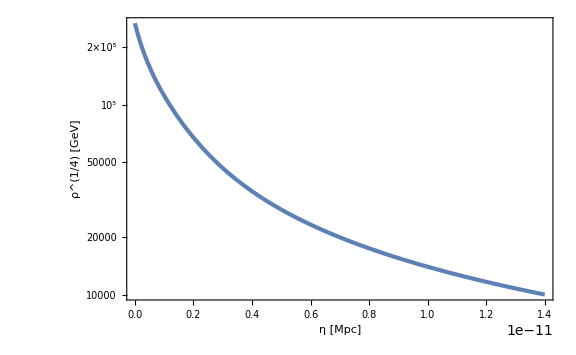

```mathematica
LogPlot[ρsol[η]^(1/4),{η,ηi,η1e4},FrameLabel->{"η [Mpc]","ρ^(1/4) [GeV]"},PlotRange->Full]
```

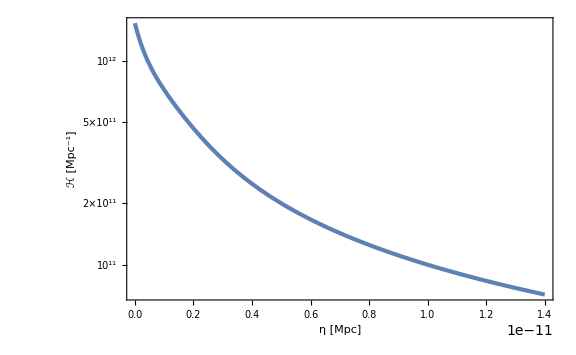

```mathematica
LogPlot[ℋsol[η],{η,ηi,η1e4},FrameLabel->{"η [Mpc]","ℋ [Mpc^-1]"},PlotRange->Full]
```

```mathematica
kscsList=Table[bgsol=NDSolve[{ρ'[η]/GeVinMpcinv==(-Sqrt[3])/Mpl(1+w[ρ[η]])a[η] ρ[η]^(3/2),a'[η]/GeVinMpcinv==Sqrt[ρ[η]/3] a[η]^2/Mpl,a[η1e4]==a1e4,ρ[η1e4]==10^(4 4)}/.{ρs->10^(5 4),σ->2},{ρ[η],a[η]},{η,ηi,η1e4}][[1]];
asol[η_]=a[η]/.bgsol;
ρsol[η_]=ρ[η]/.bgsol;
ℋsol[η_]=Sqrt[ρsol[η]]/(Sqrt[3]Mpl)asol[η]GeVinMpcinv;
{cs2min,10^3 ℋsol[η]/(2π)MpcinvinHz/.FindRoot[ρsol[η]==10^(5 4),{η,10^-12},WorkingPrecision->30]//Quiet},{cs2min,0.09,0.11,10^-3}];
```

```mathematica
kscsfit[x_]=a(x-0.1)+fs/.FindFit[kscsList,a(x-0.1)+fs,a,x]
```

1.01946+0.389821 (-0.1+x)

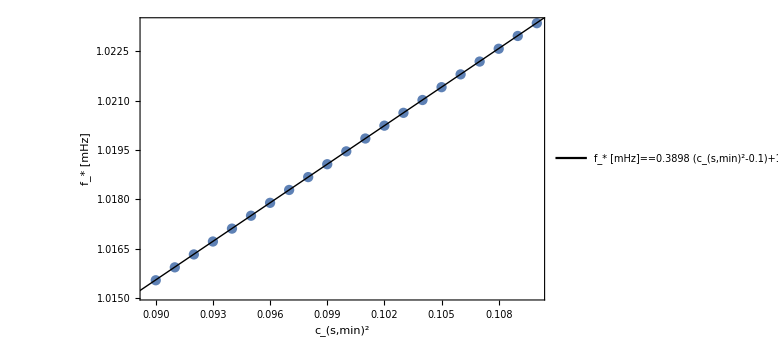

```mathematica
Show[ListPlot[kscsList,Joined->False,FrameLabel->{{"f_* [mHz]",None},{Subscript["c", "s",min]^2,Row[{Superscript[SubStar[ρ],"1/4"]=="100 TeV",",   ",σ==2}]}}],
Plot[kscsfit[x],{x,0.08,0.12},PlotStyle->{Black,Thin},PlotLegends->Placed[LineLegend[{"f_* [mHz]"==0.3898(Subscript["c", "s",min]^2-0.1)+1.019},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.65,0.15}]]]
```

```mathematica
kssigmaList=Table[bgsol=NDSolve[{ρ'[η]/GeVinMpcinv==(-Sqrt[3])/Mpl(1+w[ρ[η]])a[η] ρ[η]^(3/2),a'[η]/GeVinMpcinv==Sqrt[ρ[η]/3] a[η]^2/Mpl,a[η1e4]==a1e4,ρ[η1e4]==10^(4 4)}/.{ρs->10^(5 4),cs2min->0.1},{ρ[η],a[η]},{η,ηi,η1e4}][[1]];
asol[η_]=a[η]/.bgsol;
ρsol[η_]=ρ[η]/.bgsol;
ℋsol[η_]=Sqrt[ρsol[η]]/(Sqrt[3]Mpl)asol[η]GeVinMpcinv;
{σ,10^3 ℋsol[η]/(2π)MpcinvinHz/.FindRoot[ρsol[η]==10^(5 4),{η,10^-12},WorkingPrecision->30]//Quiet},{σ,1.9,2.1,10^-2}];
```

```mathematica
kssigmafit[x_]=a(x-2)+fs/.FindFit[kssigmaList,a(x-2)+fs,a,x]
```

1.01946-0.0578986 (-2+x)

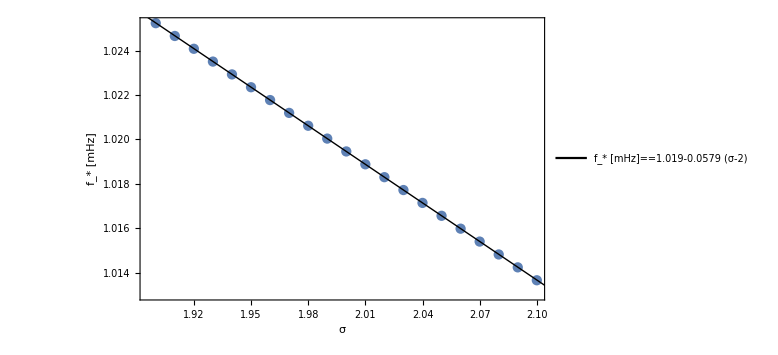

```mathematica
Show[ListPlot[kssigmaList,Joined->False,FrameLabel->{{"f_* [mHz]",None},{σ,Row[{Superscript[SubStar[ρ],"1/4"]=="100 TeV",",   ",Subscript["c", "s",min]^2==0.1}]}}],
Plot[kssigmafit[x],{x,1.8,2.2},PlotStyle->{Black,Thin},PlotLegends->Placed[LineLegend[{"f_* [mHz]"==-0.0579(σ-2)+1.019},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.35,0.15}]]]
```

```mathematica
lnkslnρsList=Table[bgsol=NDSolve[{ρ'[η]/GeVinMpcinv==(-Sqrt[3])/Mpl(1+w[ρ[η]])a[η] ρ[η]^(3/2),a'[η]/GeVinMpcinv==Sqrt[ρ[η]/3] a[η]^2/Mpl,a[η1e4]==a1e4,ρ[η1e4]==10^(4 4)}/.{ρs->10^(4lnρsQ),σ->2,cs2min->0.1},{ρ[η],a[η]},{η,ηi,η1e4}][[1]];
asol[η_]=a[η]/.bgsol;
ρsol[η_]=ρ[η]/.bgsol;
ℋsol[η_]=Sqrt[ρsol[η]]/(Sqrt[3]Mpl)asol[η]GeVinMpcinv;
{lnρsQ,Log10[10^3 ℋsol[η]/(2π)MpcinvinHz]/.FindRoot[ρsol[η]==10^(4lnρsQ),{η,10^-12},WorkingPrecision->30]//Quiet},{lnρsQ,4.9,5.1,10^-2}];
```

```mathematica
ksρsfit[x_]=fs 10^(a(Log10[x]-5))/.FindFit[lnkslnρsList,a(x-5)+Log10[fs],a,x]
```

1.01946 10^(0.999998 (-5+Log[x]/Log[10]))

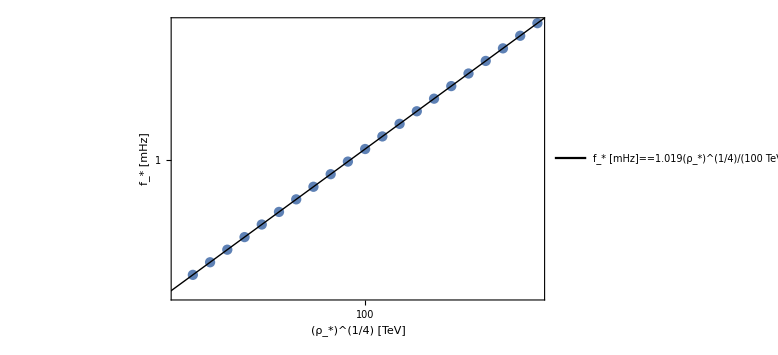

```mathematica
Show[ListLogLogPlot[Map[{10^(#[[1]]-3),10^(#[[2]])}&,lnkslnρsList],Joined->False,FrameLabel->{{"f_* [mHz]",None},{"(ρ_*)^(1/4) [TeV]",Row[{Subscript["c", "s",min]^2==0.1,",   ",σ==2}]}}],
LogLogPlot[ksρsfit[x 10^3],{x,10^1.8,10^2.2},PlotStyle->{Black,Thin},PlotLegends->Placed[LineLegend[{"f_* [mHz]"==Row[{1.019,(Superscript[SubStar[ρ],"1/4"]/("100 TeV"))}]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.65,0.15}]]]
```

```mathematica
ksρscsmList=Table[bgsol=NDSolve[{ρ'[η]/GeVinMpcinv==(-Sqrt[3])/Mpl(1+w[ρ[η]])a[η] ρ[η]^(3/2),a'[η]/GeVinMpcinv==Sqrt[ρ[η]/3] a[η]^2/Mpl,a[η1e4]==a1e4,ρ[η1e4]==10^(4 4)}/.{ρs->10^(4lnρsQ),σ->2,cs2min->0.09},{ρ[η],a[η]},{η,ηi,η1e4}][[1]];
asol[η_]=a[η]/.bgsol;
ρsol[η_]=ρ[η]/.bgsol;
ℋsol[η_]=Sqrt[ρsol[η]]/(Sqrt[3]Mpl)asol[η]GeVinMpcinv;
{10^(lnρsQ-3),10^3 ℋsol[η]/(2π)MpcinvinHz/.FindRoot[ρsol[η]==10^(4lnρsQ),{η,10^-12},WorkingPrecision->30]//Quiet},{lnρsQ,4.9,5.1,10^-2}];
```

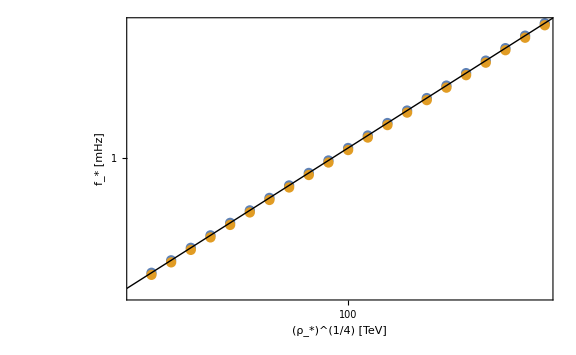

```mathematica
Show[ListLogLogPlot[{Map[{10^(#[[1]]-3),10^(#[[2]])}&,lnkslnρsList],ksρscsmList},Joined->False,FrameLabel->{{"f_* [mHz]",None},{"(ρ_*)^(1/4) [TeV]",Row[{Subscript["c", s,min]^2==0.1,",   ",σ==2}]}}],
LogLogPlot[ksρsfit[x 10^3],{x,10^1.8,10^2.2},PlotStyle->{Black,Thin}]]
```

## Fisher σ=2

```mathematica
$Assumptions={A>0};
```

```mathematica
MIDNIGHT=RGBColor["#2C3E50"]
```

RGBColor[0.17254901960784313, 0.24313725490196078, 0.3137254901960784]

```mathematica
GWList=Import["dataIGWS_17012024/17012024gws_julia_csmin=1.000e-01_sigms=2.000e+00_rhoc=1.000e-08_deltacsmin=0.000e+00_deltasigma=0.000e+00.dat"];
GWListcsp=Import["dataIGWS_17012024/17012024gws_julia_csmin=1.100e-01_sigms=2.000e+00_rhoc=1.000e-08_deltacsmin=1.000e-02_deltasigma=0.000e+00.dat"];
GWListcsm=Import["dataIGWS_17012024/17012024gws_julia_csmin=9.000e-02_sigms=2.000e+00_rhoc=1.000e-08_deltacsmin=-1.000e-02_deltasigma=0.000e+00.dat"];
GWListsp=Import["dataIGWS_17012024/17012024gws_julia_csmin=1.000e-01_sigms=2.100e+00_rhoc=1.000e-08_deltacsmin=0.000e+00_deltasigma=1.000e-01.dat"];
GWListsm=Import["dataIGWS_17012024/17012024gws_julia_csmin=1.000e-01_sigms=1.900e+00_rhoc=1.000e-08_deltacsmin=0.000e+00_deltasigma=-1.000e-01.dat"];
```

```mathematica
dcs=0.01;
ds=0.1;
```

```mathematica
GWint[f_]=Interpolation[GWList][f];
GWintcsp[f_]=Interpolation[GWListcsp][f];
GWintcsm[f_]=Interpolation[GWListcsm][f];
GWintsp[f_]=Interpolation[GWListsp][f];
GWintsm[f_]=Interpolation[GWListsm][f];
```

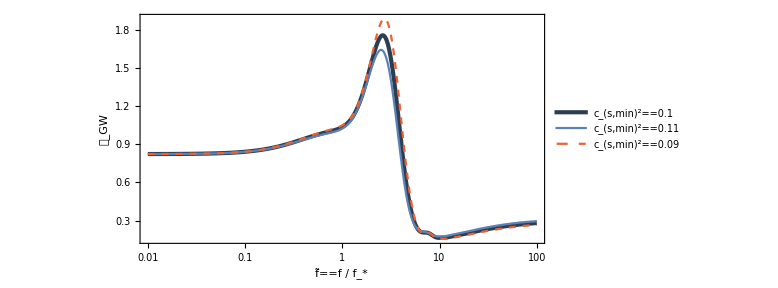

```mathematica
LogLinearPlot[{GWint[f],GWintcsp[f],GWintcsm[f]},{f,10^-2,10^2},FrameLabel->{{Subscript[𝒯, GW],None},{OverTilde[f]=="f / f_*",σ==2}},PlotStyle->{{AbsoluteThickness[3],MIDNIGHT},{Color[1]},{Color[4],Dashed}},PlotLegends->Placed[LineLegend[{Subscript[c, "s,min"]^2==0.1,Subscript[c, "s,min"]^2==0.11,Subscript[c, "s,min"]^2==0.09},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.2,0.75}],AspectRatio->1/2]
```

```mathematica
FindMaximum[GWint[f],{f,2}]
```

{1.75734,{f→2.60395}}

```mathematica
GWintcsp[3.45]-GWintcsm[3.45]
```

-0.369879

```mathematica
GWintcsp[2.6]-GWintcsm[2.6]
```

-0.24205

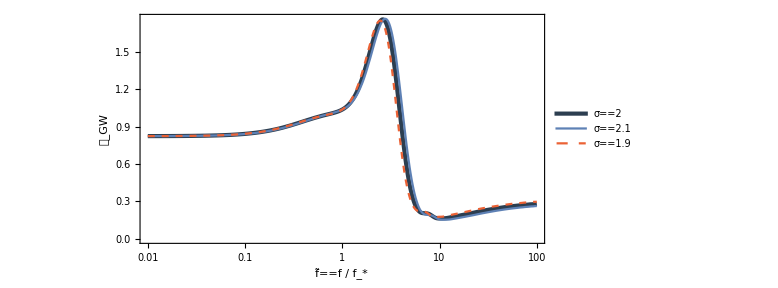

```mathematica
LogLinearPlot[{GWint[f],GWintsp[f],GWintsm[f]},{f,10^-2,10^2},FrameLabel->{{Subscript[𝒯, GW],None},{OverTilde[f]=="f / f_*",Subscript[c, "s,min"]^2==0.1}},PlotStyle->{{AbsoluteThickness[3],MIDNIGHT},{Color[1]},{Color[4],Dashed}},PlotLegends->Placed[LineLegend[{σ==2,σ==2.1,σ==1.9},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.2,0.75}],AspectRatio->1/2]
```

```mathematica
dGWdcs[f_]=(GWintcsp[f]-GWintcsm[f])/(2dcs);
dGWds[f_]=(GWintsp[f]-GWintsm[f])/(2ds);
```

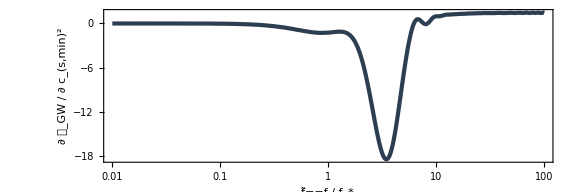

```mathematica
LogLinearPlot[dGWdcs[f],{f,10^-2,10^2},PlotRange->Full,AspectRatio->1/3,FrameLabel->{OverTilde[f]=="f / f_*",Row[{"∂ 𝒯_GW / ∂ ", Subscript[c, "s,min"]^2}]},PlotStyle->{AbsoluteThickness[3],MIDNIGHT}]
```

```mathematica
FindMinimum[dGWdcs[f],{f,3}]
```

{-18.494,{f→3.45023}}

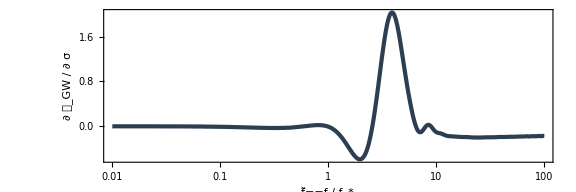

```mathematica
LogLinearPlot[dGWds[f],{f,10^-2,10^2},PlotRange->Full,AspectRatio->1/3,FrameLabel->{OverTilde[f]=="f / f_*","∂ 𝒯_GW / ∂ σ"},PlotStyle->{AbsoluteThickness[3],MIDNIGHT}]
```

```mathematica
L=2.5 10^9(*m*);
Tobs=1 60 60 24 365(*s*)
fs=10^-3(*s^-1*);
Ωrh2=4.2 10^-5;
c=299792458(*m/s*);
pc=3.086 10^16(*m*);
Hnorm=(100 10^3)/(10^6 pc)(*s*)
fmax=10^2;
fmin=10^-2;
```

31536000

3.24044×10^-18

```mathematica
RAA[f_]=9/20 1/(1+0.7((2π f L)/c)^2);
REE[f_]=RAA[f];
RTT[f_]=9/20((2π f L)/c)^6/(1.8 10^3+0.7((2π f L)/c)^8);
```

```mathematica
calRAA[f_]=16 Sin[(2π f L)/c]^2((2π f L)/c)^2 RAA[f];
calREE[f_]=16 Sin[(2π f L)/c]^2((2π f L)/c)^2 REE[f];
calRTT[f_]=16 Sin[(2π f L)/c]^2((2π f L)/c)^2 RTT[f];
```

```mathematica
PIMS[f_]=P^2 10^(-12 2)(1+((2 10^-3)/f)^4)((2π f)/c)^2/.{P->15}(*s*);
Pacc[f_]=A^2 10^(-15 2)(1+((0.4 10^-3)/f)^2)(1+(f/(8 10^-3))^4)(1/(2π f))^4((2π f)/c)^2/.{A->3}(*s*);
```

```mathematica
NAA[f_]=8 Sin[(2π f L)/c]^2(4(1+Cos[(2π f L)/c]+Cos[(2π f L)/c]^2)Pacc[f]+(2+Cos[(2π f L)/c])PIMS[f]);
NEE[f_]=NAA[f];
NTT[f_]=16 Sin[(2π f L)/c]^2(1(1-Cos[(2π f L)/c])^2 Pacc[f]+(1-Cos[(2π f L)/c])PIMS[f]);
```

```mathematica
SnAA[f_]=NAA[f]/calRAA[f];
SnEE[f_]=NEE[f]/calREE[f];
SnTT[f_]=NTT[f]/calRTT[f];
```

```mathematica
ΩnAAh2[f_]=(4 π^2 f^3)/(3 Hnorm^2)SnAA[f];
ΩnEEh2[f_]=(4 π^2 f^3)/(3 Hnorm^2)SnEE[f];
ΩnTTh2[f_]=(4 π^2 f^3)/(3 Hnorm^2)SnTT[f];
```

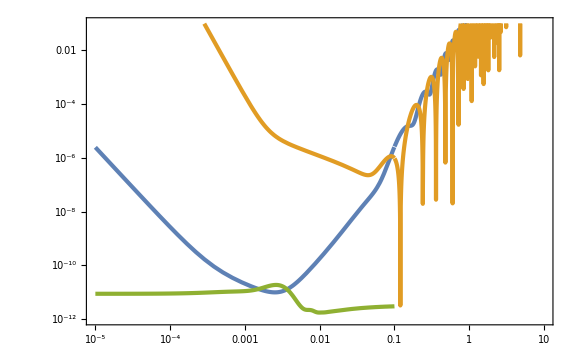

```mathematica
LogLogPlot[{ΩnAAh2[f],ΩnTTh2[f],GWint[f/fs]Ωrh2 (5 10^-4)^2 UnitStep[f/fs-fmin,fmax-f/fs]},{f,10^-5,10},PlotRange->{10^-12,10^-1}]
```

```mathematica
NIntegrate[(dGWds[ft]dGWds[ft])/ΩnAAh2[ft fs]^2+(dGWds[ft]dGWds[ft])/ΩnEEh2[ft fs]^2+(dGWds[ft]dGWds[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax}]
```

6.48986×10^22

```mathematica
NIntegrate[(dGWds[ft/fs]dGWds[ft/fs])/ΩnAAh2[ft]^2+(dGWds[ft/fs]dGWds[ft/fs])/ΩnEEh2[ft]^2+(dGWds[ft/fs]dGWds[ft/fs])/ΩnTTh2[ft]^2,{ft,fs fmin,fs fmax}]
```

6.48986×10^19

```mathematica
dGWdlnf[ft_]=-ft GWint'[ft];
```

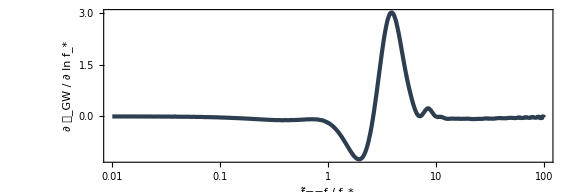

```mathematica
LogLinearPlot[dGWdlnf[f],{f,10^-2,10^2},PlotRange->Full,AspectRatio->1/3,FrameLabel->{OverTilde[f]=="f / f_*","∂ 𝒯_GW / ∂ ln f_*"},PlotStyle->{AbsoluteThickness[3],MIDNIGHT}]
```

### weak

```mathematica
As=10^-4;
norm=1/2 Tobs Ωrh2^2 As^4 fs
```

2.78148×10^-21

```mathematica
Fab=norm{{NIntegrate[(dGWdcs[ft]dGWdcs[ft])/ΩnAAh2[ft fs]^2+(dGWdcs[ft]dGWdcs[ft])/ΩnEEh2[ft fs]^2+(dGWdcs[ft]dGWdcs[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWdcs[ft]dGWds[ft])/ΩnAAh2[ft fs]^2+(dGWdcs[ft]dGWds[ft])/ΩnEEh2[ft fs]^2+(dGWdcs[ft]dGWds[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWdcs[ft]dGWdlnf[ft])/ΩnAAh2[ft fs]^2+(dGWdcs[ft]dGWdlnf[ft])/ΩnEEh2[ft fs]^2+(dGWdcs[ft]dGWdlnf[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12]},
{NIntegrate[(dGWds[ft]dGWdcs[ft])/ΩnAAh2[ft fs]^2+(dGWds[ft]dGWdcs[ft])/ΩnEEh2[ft fs]^2+(dGWds[ft]dGWdcs[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWds[ft]dGWds[ft])/ΩnAAh2[ft fs]^2+(dGWds[ft]dGWds[ft])/ΩnEEh2[ft fs]^2+(dGWds[ft]dGWds[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWds[ft]dGWdlnf[ft])/ΩnAAh2[ft fs]^2+(dGWds[ft]dGWdlnf[ft])/ΩnEEh2[ft fs]^2+(dGWds[ft]dGWdlnf[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12]},
{NIntegrate[(dGWdlnf[ft]dGWdcs[ft])/ΩnAAh2[ft fs]^2+(dGWdlnf[ft]dGWdcs[ft])/ΩnEEh2[ft fs]^2+(dGWdlnf[ft]dGWdcs[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWdlnf[ft]dGWds[ft])/ΩnAAh2[ft fs]^2+(dGWdlnf[ft]dGWds[ft])/ΩnEEh2[ft fs]^2+(dGWdlnf[ft]dGWds[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWdlnf[ft]dGWdlnf[ft])/ΩnAAh2[ft fs]^2+(dGWdlnf[ft]dGWdlnf[ft])/ΩnEEh2[ft fs]^2+(dGWdlnf[ft]dGWdlnf[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12]}};
```

```mathematica
Fab//MatrixForm
```

(22503.1 | -1576.8 | -2243.26
-1576.8 | 180.514 | 276.057
-2243.26 | 276.057 | 428.45)

```mathematica
Inverse[Table[Fab[[i,j]],{i,2},{j,2}]]//MatrixForm
```

(0.000114552 | 0.00100062
0.00100062 | 0.0142802)

```mathematica
Cab=Inverse[Fab];Cab//MatrixForm
```

(0.000236442 | 0.0117446 | -0.0063293
0.0117446 | 0.961315 | -0.557898
-0.0063293 | -0.557898 | 0.328658)

```mathematica
a21=Sqrt[(Cab[[2,2]]+Cab[[1,1]])/2+Sqrt[(Cab[[2,2]]-Cab[[1,1]])^2/4+Cab[[2,1]]^2]]//Simplify
b21=Sqrt[(Cab[[2,2]]+Cab[[1,1]])/2-Sqrt[(Cab[[2,2]]-Cab[[1,1]])^2/4+Cab[[2,1]]^2]]//Simplify
θ21=ArcTan[(2Cab[[2,1]])/(Cab[[2,2]]-Cab[[1,1]])]/2//Simplify
a23=Sqrt[(Cab[[2,2]]+Cab[[3,3]])/2+Sqrt[(Cab[[2,2]]-Cab[[3,3]])^2/4+Cab[[2,3]]^2]]//Simplify
b23=Sqrt[(Cab[[2,2]]+Cab[[3,3]])/2-Sqrt[(Cab[[2,2]]-Cab[[3,3]])^2/4+Cab[[2,3]]^2]]//Simplify
θ23=ArcTan[(2Cab[[2,3]])/(Cab[[2,2]]-Cab[[3,3]])]/2//Simplify
a31=Sqrt[(Cab[[3,3]]+Cab[[1,1]])/2+Sqrt[(Cab[[3,3]]-Cab[[1,1]])^2/4+Cab[[3,1]]^2]]//Simplify
b31=Sqrt[(Cab[[3,3]]+Cab[[1,1]])/2-Sqrt[(Cab[[3,3]]-Cab[[1,1]])^2/4+Cab[[3,1]]^2]]//Simplify
θ31=ArcTan[(2Cab[[3,1]])/(Cab[[3,3]]-Cab[[1,1]])]/2//Simplify
```

0.98054

0.00964058

0.0122178

1.13416

0.0604038

-0.527497

0.573393

0.0107009

-0.0192624

```mathematica
α1=1.52;
α2=2.48;
```

```mathematica
pad={{150,10},{100,50}};
```

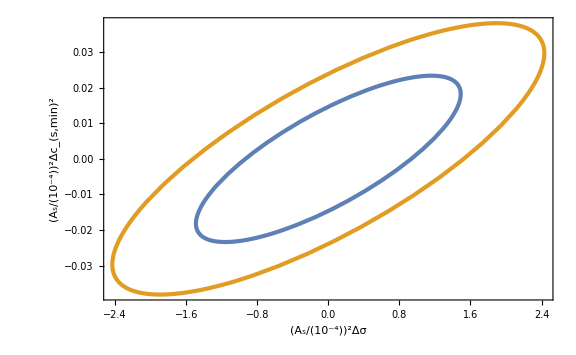

```mathematica
sigmacs=ParametricPlot[{α1 RotationMatrix[θ21].{a21 Cos[t],b21 Sin[t]},α2 RotationMatrix[θ21].{a21 Cos[t],b21 Sin[t]}},{t,0,2π},FrameLabel->{{Row[{(Subscript[A, "s"]/("10^-4"))^("2"),Subscript[Δc, "s",min]^2}],None},{Row[{(Subscript[A, "s"]/("10^-4"))^("2"),Δσ}],SubStar[f]=="10^-3 Hz"}},ImagePadding->pad]
```

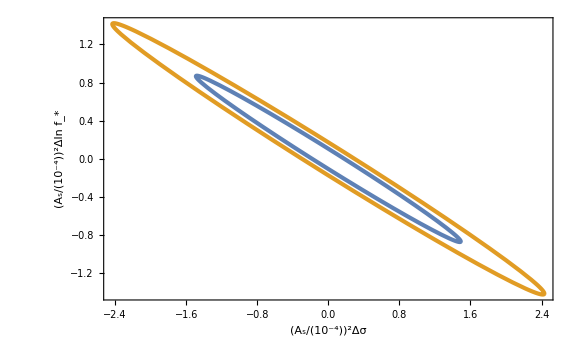

```mathematica
sigmafs=ParametricPlot[{α1 RotationMatrix[θ23].{a23 Cos[t],b23 Sin[t]},α2 RotationMatrix[θ23].{a23 Cos[t],b23 Sin[t]}},{t,0,2π},FrameLabel->{{Row[{(Subscript[A, "s"]/("10^-4"))^("2"),Δln SubStar[f]}],None},{Row[{(Subscript[A, "s"]/("10^-4"))^("2"),Δσ}],SubStar[f]=="10^-3 Hz"}},ImagePadding->pad]
```

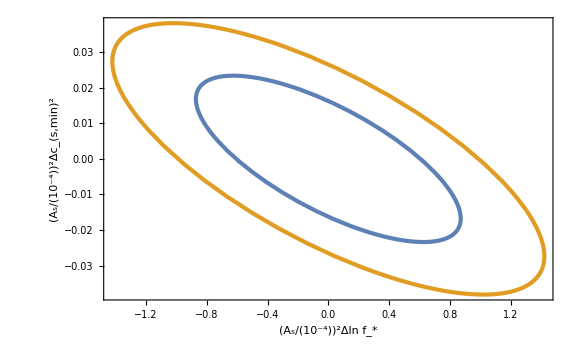

```mathematica
fscs=ParametricPlot[{α1 RotationMatrix[θ31].{a31 Cos[t],b31 Sin[t]},α2 RotationMatrix[θ31].{a31 Cos[t],b31 Sin[t]}},{t,0,2π},FrameLabel->{{Row[{(Subscript[A, "s"]/("10^-4"))^("2"),Subscript[Δc, "s",min]^2}],None},{Row[{(Subscript[A, "s"]/("10^-4"))^("2"),Δln SubStar[f]}],SubStar[f]=="10^-3 Hz"}},ImagePadding->pad]
```

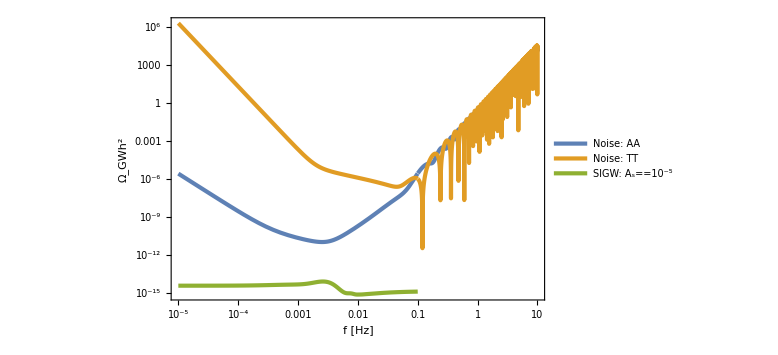

```mathematica
LogLogPlot[{ΩnAAh2[f],ΩnTTh2[f],GWint[f/fs]Ωrh2 As^2 UnitStep[f/fs-fmin,fmax-f/fs]},{f,10^-5,10},FrameLabel->{"f [Hz]","Ω_GWh^2"},PlotLegends->Placed[LineLegend[{"Noise: AA","Noise: TT",Row[{"SIGW: ",Subscript[A, "s"]=="10^-5"}]},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.55,0.8}]]
```

### strong

```mathematica
norm=1/2 Tobs fs 3
```

47304

```mathematica
Fab=norm{{NIntegrate[(dGWdcs[ft]dGWdcs[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWdcs[ft]dGWds[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWdcs[ft]dGWdlnf[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12]},
{NIntegrate[(dGWds[ft]dGWdcs[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWds[ft]dGWds[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWds[ft]dGWdlnf[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12]},
{NIntegrate[(dGWdlnf[ft]dGWdcs[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWdlnf[ft]dGWds[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWdlnf[ft]dGWdlnf[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12]}};
```

```mathematica
Fab//MatrixForm
```

(1.75099×10^8 | -2.28098×10^7 | -1.06489×10^7
-2.28098×10^7 | 3.08093×10^6 | 1.56628×10^6
-1.06489×10^7 | 1.56628×10^6 | 1.69296×10^6)

```mathematica
Inverse[Table[Fab[[i,j]],{i,2},{j,2}]]//MatrixForm
```

(1.60598×10^-7 | 1.18899×10^-6
1.18899×10^-6 | 9.12729×10^-6)

```mathematica
Cab=Inverse[Fab];Cab//MatrixForm
```

(1.91338×10^-7 | 1.51932×10^-6 | -2.02099×10^-7
1.51932×10^-6 | 0.000012677 | -2.17172×10^-6
-2.02099×10^-7 | -2.17172×10^-6 | 1.32867×10^-6)

```mathematica
a21=Sqrt[(Cab[[2,2]]+Cab[[1,1]])/2+Sqrt[(Cab[[2,2]]-Cab[[1,1]])^2/4+Cab[[2,1]]^2]]//Simplify
b21=Sqrt[(Cab[[2,2]]+Cab[[1,1]])/2-Sqrt[(Cab[[2,2]]-Cab[[1,1]])^2/4+Cab[[2,1]]^2]]//Simplify
θ21=ArcTan[(2Cab[[2,1]])/(Cab[[2,2]]-Cab[[1,1]])]/2//Simplify
a23=Sqrt[(Cab[[2,2]]+Cab[[3,3]])/2+Sqrt[(Cab[[2,2]]-Cab[[3,3]])^2/4+Cab[[2,3]]^2]]//Simplify
b23=Sqrt[(Cab[[2,2]]+Cab[[3,3]])/2-Sqrt[(Cab[[2,2]]-Cab[[3,3]])^2/4+Cab[[2,3]]^2]]//Simplify
θ23=ArcTan[(2Cab[[2,3]])/(Cab[[2,2]]-Cab[[3,3]])]/2//Simplify
a31=Sqrt[(Cab[[3,3]]+Cab[[1,1]])/2+Sqrt[(Cab[[3,3]]-Cab[[1,1]])^2/4+Cab[[3,1]]^2]]//Simplify
b31=Sqrt[(Cab[[3,3]]+Cab[[1,1]])/2-Sqrt[(Cab[[3,3]]-Cab[[1,1]])^2/4+Cab[[3,1]]^2]]//Simplify
θ31=ArcTan[(2Cab[[3,1]])/(Cab[[3,3]]-Cab[[1,1]])]/2//Simplify
```

0.00358597

0.0000954892

0.119365

0.0036164

0.000962948

-0.182769

0.0011677

0.000395593

-0.170735

```mathematica
α1=1.52;
α2=2.48;
```

```mathematica
pad={{200,10},{100,10}};
```

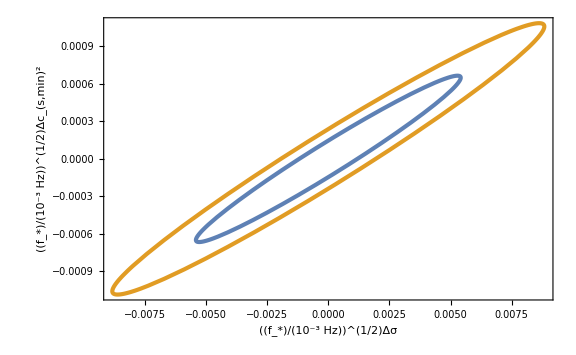

```mathematica
ParametricPlot[{α1 RotationMatrix[θ21].{a21 Cos[t],b21 Sin[t]},α2 RotationMatrix[θ21].{a21 Cos[t],b21 Sin[t]}},{t,0,2π},FrameLabel->{{Row[{(SubStar[f]/("10^-3 Hz"))^("1/2"),Subscript[Δc, "s",min]^2}],None},{Row[{(SubStar[f]/("10^-3 Hz"))^("1/2"),Δσ}],None}},ImagePadding->pad]
```

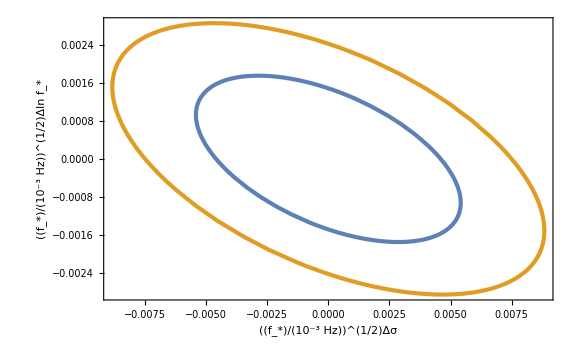

```mathematica
ParametricPlot[{α1 RotationMatrix[θ23].{a23 Cos[t],b23 Sin[t]},α2 RotationMatrix[θ23].{a23 Cos[t],b23 Sin[t]}},{t,0,2π},FrameLabel->{{Row[{(SubStar[f]/("10^-3 Hz"))^("1/2"),Δln SubStar[f]}],None},{Row[{(SubStar[f]/("10^-3 Hz"))^("1/2"),Δσ}],None}},ImagePadding->pad]
```

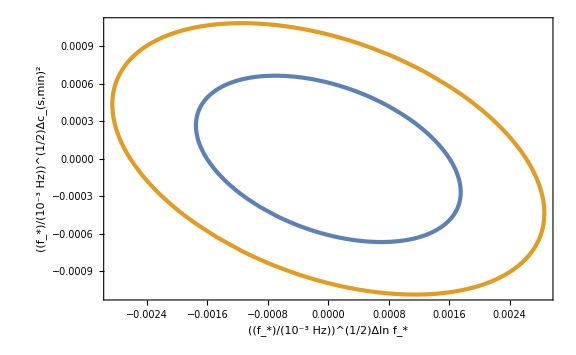

```mathematica
ParametricPlot[{α1 RotationMatrix[θ31].{a31 Cos[t],b31 Sin[t]},α2 RotationMatrix[θ31].{a31 Cos[t],b31 Sin[t]}},{t,0,2π},FrameLabel->{{Row[{(SubStar[f]/("10^-3 Hz"))^("1/2"),Subscript[Δc, "s",min]^2}],None},{Row[{(SubStar[f]/("10^-3 Hz"))^("1/2"),Δln SubStar[f]}],None}},ImagePadding->pad]
```

```mathematica
LogLogPlot[{ΩnAAh2[f],ΩnTTh2[f],GWint[f/fs]Ωrh2 As^2 UnitStep[f/fs-fmin,fmax-f/fs]},{f,10^-5,10},FrameLabel->{"f [Hz]","Ω_GWh^2"},PlotLegends->Placed[LineLegend[{"Noise: AA","Noise: TT",Row[{"SIGW: ",Subscript[A, "s"]=="10^-5"}]},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.55,0.8}]]
```

-Graphics-

## Fisher σ=5

```mathematica
$Assumptions={A>0};
```

```mathematica
MIDNIGHT=RGBColor["#2C3E50"]
```

RGBColor[0.17254901960784313, 0.24313725490196078, 0.3137254901960784]

```mathematica
GWList=Import["new_case01032024/01032024gws_julia_csmin=1.000e-01_sigms=5.000e+00_rhoc=1.000e-08_deltacsmin=0.000e+00_deltasigma=0.000e+00.dat"];
GWListcsp=Import["new_case01032024/01032024gws_julia_csmin=1.100e-01_sigms=5.000e+00_rhoc=1.000e-08_deltacsmin=1.000e-02_deltasigma=0.000e+00.dat"];
GWListcsm=Import["new_case01032024/01032024gws_julia_csmin=9.000e-02_sigms=5.000e+00_rhoc=1.000e-08_deltacsmin=-1.000e-02_deltasigma=0.000e+00.dat"];
GWListsp=Import["new_case01032024/01032024gws_julia_csmin=1.000e-01_sigms=5.100e+00_rhoc=1.000e-08_deltacsmin=0.000e+00_deltasigma=1.000e-01.dat"];
GWListsm=Import["new_case01032024/01032024gws_julia_csmin=1.000e-01_sigms=4.900e+00_rhoc=1.000e-08_deltacsmin=0.000e+00_deltasigma=-1.000e-01.dat"];
```

```mathematica
dcs=0.01;
ds=0.1;
```

```mathematica
GWint[f_]=Interpolation[GWList][f];
GWintcsp[f_]=Interpolation[GWListcsp][f];
GWintcsm[f_]=Interpolation[GWListcsm][f];
GWintsp[f_]=Interpolation[GWListsp][f];
GWintsm[f_]=Interpolation[GWListsm][f];
```

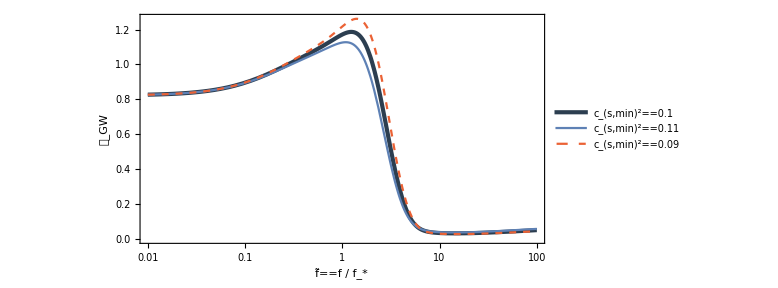

```mathematica
LogLinearPlot[{GWint[f],GWintcsp[f],GWintcsm[f]},{f,10^-2,10^2},FrameLabel->{{Subscript[𝒯, GW],None},{OverTilde[f]=="f / f_*",σ==5}},PlotStyle->{{AbsoluteThickness[3],MIDNIGHT},{Color[1]},{Color[4],Dashed}},PlotLegends->Placed[LineLegend[{Subscript["c", "s,min"]^2==0.1,Subscript["c", "s,min"]^2==0.11,Subscript["c", "s,min"]^2==0.09},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.2,0.3}],AspectRatio->1/2]
```

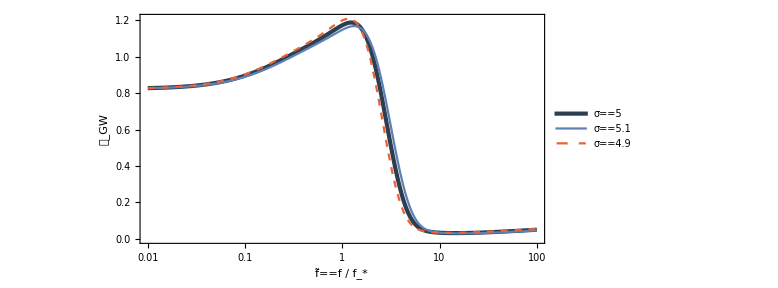

```mathematica
LogLinearPlot[{GWint[f],GWintsp[f],GWintsm[f]},{f,10^-2,10^2},FrameLabel->{{Subscript[𝒯, GW],None},{OverTilde[f]=="f / f_*",Subscript["c", "s,min"]^2==0.1}},PlotStyle->{{AbsoluteThickness[3],MIDNIGHT},{Color[1]},{Color[4],Dashed}},PlotLegends->Placed[LineLegend[{σ==5,σ==5.1,σ==4.9},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.2,0.3}],AspectRatio->1/2]
```

```mathematica
dGWdcs[f_]=(GWintcsp[f]-GWintcsm[f])/(2dcs);
dGWds[f_]=(GWintsp[f]-GWintsm[f])/(2ds);
```

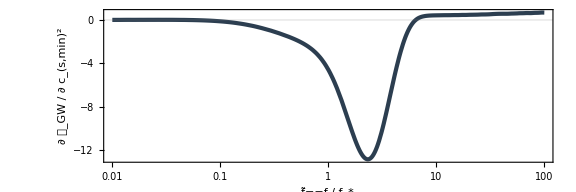

```mathematica
LogLinearPlot[dGWdcs[f],{f,10^-2,10^2},PlotRange->Full,AspectRatio->1/3,FrameLabel->{OverTilde[f]=="f / f_*",Row[{"∂ 𝒯_GW / ∂ ", Subscript["c", "s,min"]^2}]},PlotStyle->{AbsoluteThickness[3],MIDNIGHT},GridLines->{None,{0}}]
```

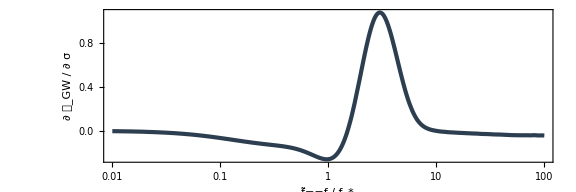

```mathematica
LogLinearPlot[dGWds[f],{f,10^-2,10^2},PlotRange->Full,AspectRatio->1/3,FrameLabel->{OverTilde[f]=="f / f_*","∂ 𝒯_GW / ∂ σ"},PlotStyle->{AbsoluteThickness[3],MIDNIGHT}]
```

```mathematica
L=2.5 10^9(*m*);
Tobs=1 60 60 24 365(*s*)
fs=10^-3(*s^-1*);
Ωrh2=4.2 10^-5;
c=299792458(*m/s*);
pc=3.086 10^16(*m*);
Hnorm=(100 10^3)/(10^6 pc)(*s*)
fmax=10^2;
fmin=10^-2;
```

31536000

3.24044×10^-18

```mathematica
RAA[f_]=9/20 1/(1+0.7((2π f L)/c)^2);
REE[f_]=RAA[f];
RTT[f_]=9/20((2π f L)/c)^6/(1.8 10^3+0.7((2π f L)/c)^8);
```

```mathematica
calRAA[f_]=16 Sin[(2π f L)/c]^2((2π f L)/c)^2 RAA[f];
calREE[f_]=16 Sin[(2π f L)/c]^2((2π f L)/c)^2 REE[f];
calRTT[f_]=16 Sin[(2π f L)/c]^2((2π f L)/c)^2 RTT[f];
```

```mathematica
PIMS[f_]=P^2 10^(-12 2)(1+((2 10^-3)/f)^4)((2π f)/c)^2/.{P->15}(*s*);
Pacc[f_]=A^2 10^(-15 2)(1+((0.4 10^-3)/f)^2)(1+(f/(8 10^-3))^4)(1/(2π f))^4((2π f)/c)^2/.{A->3}(*s*);
```

```mathematica
NAA[f_]=8 Sin[(2π f L)/c]^2(4(1+Cos[(2π f L)/c]+Cos[(2π f L)/c]^2)Pacc[f]+(2+Cos[(2π f L)/c])PIMS[f]);
NEE[f_]=NAA[f];
NTT[f_]=16 Sin[(2π f L)/c]^2(1(1-Cos[(2π f L)/c])^2 Pacc[f]+(1-Cos[(2π f L)/c])PIMS[f]);
```

```mathematica
SnAA[f_]=NAA[f]/calRAA[f];
SnEE[f_]=NEE[f]/calREE[f];
SnTT[f_]=NTT[f]/calRTT[f];
```

```mathematica
ΩnAAh2[f_]=(4 π^2 f^3)/(3 Hnorm^2)SnAA[f];
ΩnEEh2[f_]=(4 π^2 f^3)/(3 Hnorm^2)SnEE[f];
ΩnTTh2[f_]=(4 π^2 f^3)/(3 Hnorm^2)SnTT[f];
```

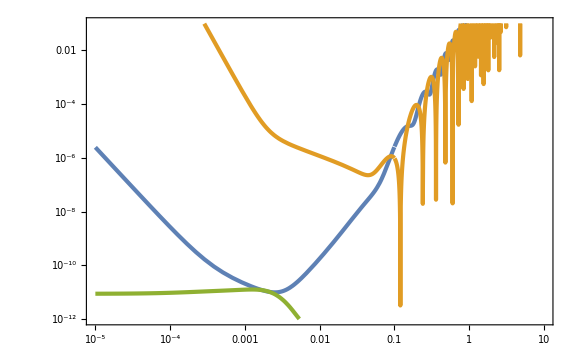

```mathematica
LogLogPlot[{ΩnAAh2[f],ΩnTTh2[f],GWint[f/fs]Ωrh2 (5 10^-4)^2 UnitStep[f/fs-fmin,fmax-f/fs]},{f,10^-5,10},PlotRange->{10^-12,10^-1}]
```

```mathematica
NIntegrate[(dGWds[ft]dGWds[ft])/ΩnAAh2[ft fs]^2+(dGWds[ft]dGWds[ft])/ΩnEEh2[ft fs]^2+(dGWds[ft]dGWds[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax}]
```

3.4304×10^22

```mathematica
NIntegrate[(dGWds[ft/fs]dGWds[ft/fs])/ΩnAAh2[ft]^2+(dGWds[ft/fs]dGWds[ft/fs])/ΩnEEh2[ft]^2+(dGWds[ft/fs]dGWds[ft/fs])/ΩnTTh2[ft]^2,{ft,fs fmin,fs fmax}]
```

3.4304×10^19

```mathematica
dGWdlnf[ft_]=-ft GWint'[ft];
```

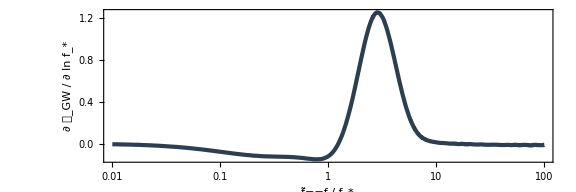

```mathematica
LogLinearPlot[dGWdlnf[f],{f,10^-2,10^2},PlotRange->Full,AspectRatio->1/3,FrameLabel->{OverTilde[f]=="f / f_*","∂ 𝒯_GW / ∂ ln f_*"},PlotStyle->{AbsoluteThickness[3],MIDNIGHT}]
```

### weak

```mathematica
As=10^-4;
norm=1/2 Tobs Ωrh2^2 As^4 fs
```

2.78148×10^-21

```mathematica
Fab=norm{{NIntegrate[(dGWdcs[ft]dGWdcs[ft])/ΩnAAh2[ft fs]^2+(dGWdcs[ft]dGWdcs[ft])/ΩnEEh2[ft fs]^2+(dGWdcs[ft]dGWdcs[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWdcs[ft]dGWds[ft])/ΩnAAh2[ft fs]^2+(dGWdcs[ft]dGWds[ft])/ΩnEEh2[ft fs]^2+(dGWdcs[ft]dGWds[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWdcs[ft]dGWdlnf[ft])/ΩnAAh2[ft fs]^2+(dGWdcs[ft]dGWdlnf[ft])/ΩnEEh2[ft fs]^2+(dGWdcs[ft]dGWdlnf[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12]},
{NIntegrate[(dGWds[ft]dGWdcs[ft])/ΩnAAh2[ft fs]^2+(dGWds[ft]dGWdcs[ft])/ΩnEEh2[ft fs]^2+(dGWds[ft]dGWdcs[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWds[ft]dGWds[ft])/ΩnAAh2[ft fs]^2+(dGWds[ft]dGWds[ft])/ΩnEEh2[ft fs]^2+(dGWds[ft]dGWds[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWds[ft]dGWdlnf[ft])/ΩnAAh2[ft fs]^2+(dGWds[ft]dGWdlnf[ft])/ΩnEEh2[ft fs]^2+(dGWds[ft]dGWdlnf[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12]},
{NIntegrate[(dGWdlnf[ft]dGWdcs[ft])/ΩnAAh2[ft fs]^2+(dGWdlnf[ft]dGWdcs[ft])/ΩnEEh2[ft fs]^2+(dGWdlnf[ft]dGWdcs[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWdlnf[ft]dGWds[ft])/ΩnAAh2[ft fs]^2+(dGWdlnf[ft]dGWds[ft])/ΩnEEh2[ft fs]^2+(dGWdlnf[ft]dGWds[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWdlnf[ft]dGWdlnf[ft])/ΩnAAh2[ft fs]^2+(dGWdlnf[ft]dGWdlnf[ft])/ΩnEEh2[ft fs]^2+(dGWdlnf[ft]dGWdlnf[ft])/ΩnTTh2[ft fs]^2,{ft,fmin,fmax},MaxRecursion->12]}};
```

```mathematica
Fab//MatrixForm
```

(14969.8 | -1053.48 | -1330.07
-1053.48 | 95.4157 | 112.355
-1330.07 | 112.355 | 134.71)

```mathematica
Inverse[Table[Fab[[i,j]],{i,2},{j,2}]]//MatrixForm
```

(0.000299548 | 0.0033073
0.0033073 | 0.0469962)

```mathematica
Cab=Inverse[Fab];Cab//MatrixForm
```

(0.111543 | -3.65073 | 4.14621
-3.65073 | 120.072 | -136.191
4.14621 | -136.191 | 154.535)

```mathematica
a21=Sqrt[(Cab[[2,2]]+Cab[[1,1]])/2+Sqrt[(Cab[[2,2]]-Cab[[1,1]])^2/4+Cab[[2,1]]^2]]//Simplify
b21=Sqrt[(Cab[[2,2]]+Cab[[1,1]])/2-Sqrt[(Cab[[2,2]]-Cab[[1,1]])^2/4+Cab[[2,1]]^2]]//Simplify
θ21=ArcTan[(2Cab[[2,1]])/(Cab[[2,2]]-Cab[[1,1]])]/2//Simplify
a23=Sqrt[(Cab[[2,2]]+Cab[[3,3]])/2+Sqrt[(Cab[[2,2]]-Cab[[3,3]])^2/4+Cab[[2,3]]^2]]//Simplify
b23=Sqrt[(Cab[[2,2]]+Cab[[3,3]])/2-Sqrt[(Cab[[2,2]]-Cab[[3,3]])^2/4+Cab[[2,3]]^2]]//Simplify
θ23=ArcTan[(2Cab[[2,3]])/(Cab[[2,2]]-Cab[[3,3]])]/2//Simplify
a31=Sqrt[(Cab[[3,3]]+Cab[[1,1]])/2+Sqrt[(Cab[[3,3]]-Cab[[1,1]])^2/4+Cab[[3,1]]^2]]//Simplify
b31=Sqrt[(Cab[[3,3]]+Cab[[1,1]])/2-Sqrt[(Cab[[3,3]]-Cab[[1,1]])^2/4+Cab[[3,1]]^2]]//Simplify
θ31=ArcTan[(2Cab[[3,1]])/(Cab[[3,3]]-Cab[[1,1]])]/2//Simplify
```

10.9628

0.0233193

-0.0303953

16.5705

0.162634

0.72247

12.4357

0.0173012

0.0268238

```mathematica
α1=1.52;
α2=2.48;
```

```mathematica
pad={{150,10},{100,50}};
```

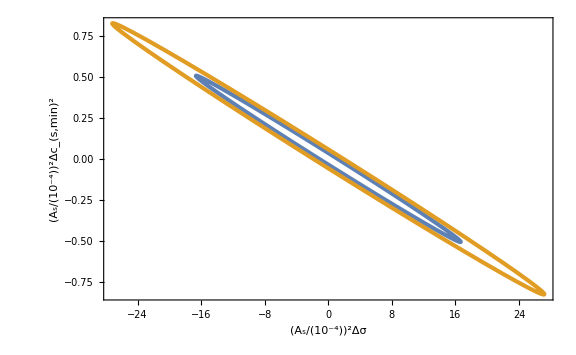

```mathematica
ParametricPlot[{α1 RotationMatrix[θ21].{a21 Cos[t],b21 Sin[t]},α2 RotationMatrix[θ21].{a21 Cos[t],b21 Sin[t]}},{t,0,2π},FrameLabel->{{Row[{(Subscript[A, "s"]/("10^-4"))^("2"),Subscript[Δc, "s",min]^2}],None},{Row[{(Subscript[A, "s"]/("10^-4"))^("2"),Δσ}],SubStar[f]=="10^-3 Hz"}},ImagePadding->pad]
```

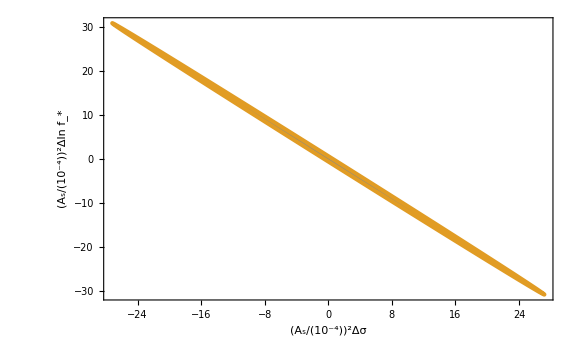

```mathematica
ParametricPlot[{α1 RotationMatrix[θ23].{b23 Cos[t],a23 Sin[t]},α2 RotationMatrix[θ23].{b23 Cos[t],a23 Sin[t]}},{t,0,2π},FrameLabel->{{Row[{(Subscript[A, "s"]/("10^-4"))^("2"),Δln SubStar[f]}],None},{Row[{(Subscript[A, "s"]/("10^-4"))^("2"),Δσ}],SubStar[f]=="10^-3 Hz"}},ImagePadding->pad]
```

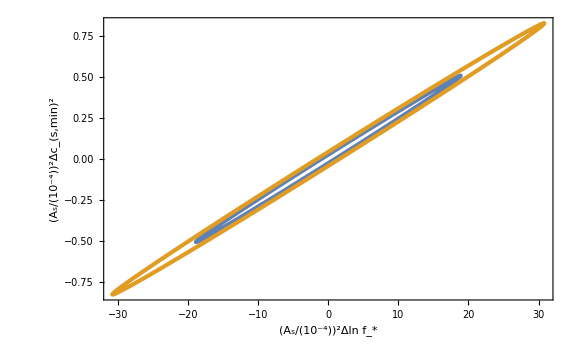

```mathematica
ParametricPlot[{α1 RotationMatrix[θ31].{a31 Cos[t],b31 Sin[t]},α2 RotationMatrix[θ31].{a31 Cos[t],b31 Sin[t]}},{t,0,2π},FrameLabel->{{Row[{(Subscript[A, "s"]/("10^-4"))^("2"),Subscript[Δc, "s",min]^2}],None},{Row[{(Subscript[A, "s"]/("10^-4"))^("2"),Δln SubStar[f]}],SubStar[f]=="10^-3 Hz"}},ImagePadding->pad]
```

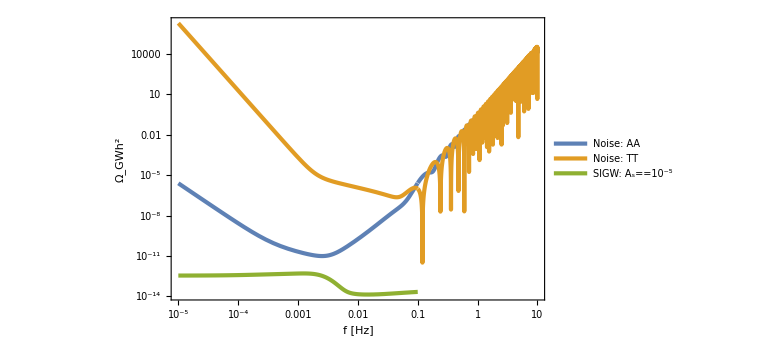

```mathematica
LogLogPlot[{ΩnAAh2[f],ΩnTTh2[f],GWint[f/fs]Ωrh2 As^2 UnitStep[f/fs-fmin,fmax-f/fs]},{f,10^-5,10},FrameLabel->{"f [Hz]","Ω_GWh^2"},PlotLegends->Placed[LineLegend[{"Noise: AA","Noise: TT",Row[{"SIGW: ",Subscript[A, "s"]=="10^-5"}]},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.55,0.8}]]
```

### strong

```mathematica
norm=1/2 Tobs fs 3
```

47304

```mathematica
Fab=norm{{NIntegrate[(dGWdcs[ft]dGWdcs[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWdcs[ft]dGWds[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWdcs[ft]dGWdlnf[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12]},
{NIntegrate[(dGWds[ft]dGWdcs[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWds[ft]dGWds[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWds[ft]dGWdlnf[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12]},
{NIntegrate[(dGWdlnf[ft]dGWdcs[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWdlnf[ft]dGWds[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12],NIntegrate[(dGWdlnf[ft]dGWdlnf[ft])/GWint[ft]^2,{ft,fmin,fmax},MaxRecursion->12]}};
```

```mathematica
Fab//MatrixForm
```

(9.22314×10^8 | -5.71814×10^7 | -2.23829×10^7
-5.71814×10^7 | 4.68598×10^6 | 2.70895×10^6
-2.23829×10^7 | 2.70895×10^6 | 2.22249×10^6)

```mathematica
Inverse[Table[Fab[[i,j]],{i,2},{j,2}]]//MatrixForm
```

(4.45337×10^-9 | 5.4343×10^-8
5.4343×10^-8 | 8.76531×10^-7)

```mathematica
Cab=Inverse[Fab];Cab//MatrixForm
```

(1.96052×10^-8 | 4.23512×10^-7 | -3.18764×10^-7
4.23512×10^-7 | 9.87122×10^-6 | -7.7666×10^-6
-3.18764×10^-7 | -7.7666×10^-6 | 6.70618×10^-6)

```mathematica
a21=Sqrt[(Cab[[2,2]]+Cab[[1,1]])/2+Sqrt[(Cab[[2,2]]-Cab[[1,1]])^2/4+Cab[[2,1]]^2]]//Simplify
b21=Sqrt[(Cab[[2,2]]+Cab[[1,1]])/2-Sqrt[(Cab[[2,2]]-Cab[[1,1]])^2/4+Cab[[2,1]]^2]]//Simplify
θ21=ArcTan[(2Cab[[2,1]])/(Cab[[2,2]]-Cab[[1,1]])]/2//Simplify
a23=Sqrt[(Cab[[2,2]]+Cab[[3,3]])/2+Sqrt[(Cab[[2,2]]-Cab[[3,3]])^2/4+Cab[[2,3]]^2]]//Simplify
b23=Sqrt[(Cab[[2,2]]+Cab[[3,3]])/2-Sqrt[(Cab[[2,2]]-Cab[[3,3]])^2/4+Cab[[2,3]]^2]]//Simplify
θ23=ArcTan[(2Cab[[2,3]])/(Cab[[2,2]]-Cab[[3,3]])]/2//Simplify
a31=Sqrt[(Cab[[3,3]]+Cab[[1,1]])/2+Sqrt[(Cab[[3,3]]-Cab[[1,1]])^2/4+Cab[[3,1]]^2]]//Simplify
b31=Sqrt[(Cab[[3,3]]+Cab[[1,1]])/2-Sqrt[(Cab[[3,3]]-Cab[[1,1]])^2/4+Cab[[3,1]]^2]]//Simplify
θ31=ArcTan[(2Cab[[3,1]])/(Cab[[3,3]]-Cab[[1,1]])]/2//Simplify
```

0.00314474

0.0000378458

0.0428836

0.00402677

0.000602094

-0.684894

0.00259256

0.0000666583

-0.0475286

```mathematica
α1=1.52;
α2=2.48;
```

```mathematica
pad={{200,10},{100,10}};
```

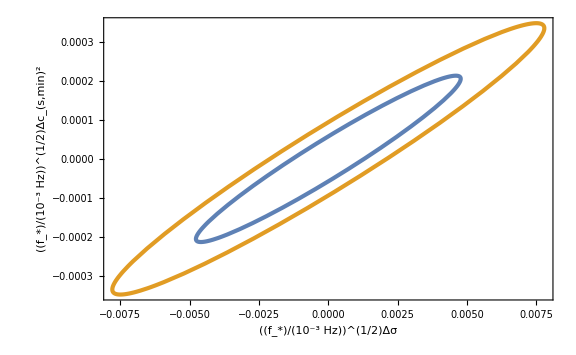

```mathematica
ParametricPlot[{α1 RotationMatrix[θ21].{a21 Cos[t],b21 Sin[t]},α2 RotationMatrix[θ21].{a21 Cos[t],b21 Sin[t]}},{t,0,2π},FrameLabel->{{Row[{(SubStar[f]/("10^-3 Hz"))^("1/2"),Subscript[Δc, "s",min]^2}],None},{Row[{(SubStar[f]/("10^-3 Hz"))^("1/2"),Δσ}],None}},ImagePadding->pad]
```

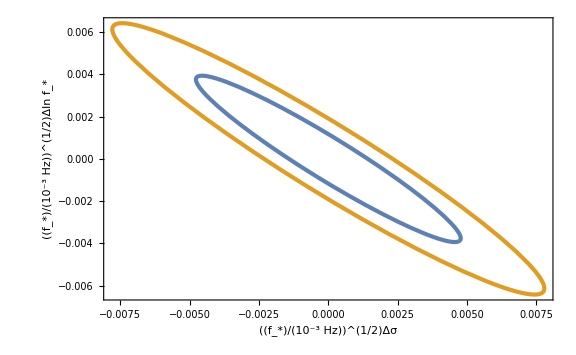

```mathematica
ParametricPlot[{α1 RotationMatrix[θ23].{a23 Cos[t],b23 Sin[t]},α2 RotationMatrix[θ23].{a23 Cos[t],b23 Sin[t]}},{t,0,2π},FrameLabel->{{Row[{(SubStar[f]/("10^-3 Hz"))^("1/2"),Δln SubStar[f]}],None},{Row[{(SubStar[f]/("10^-3 Hz"))^("1/2"),Δσ}],None}},ImagePadding->pad]
```

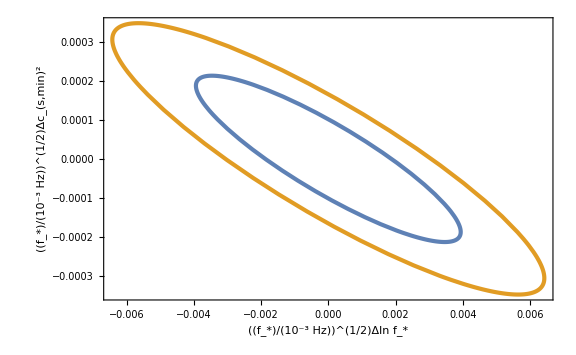

```mathematica
ParametricPlot[{α1 RotationMatrix[θ31].{a31 Cos[t],b31 Sin[t]},α2 RotationMatrix[θ31].{a31 Cos[t],b31 Sin[t]}},{t,0,2π},FrameLabel->{{Row[{(SubStar[f]/("10^-3 Hz"))^("1/2"),Subscript[Δc, "s",min]^2}],None},{Row[{(SubStar[f]/("10^-3 Hz"))^("1/2"),Δln SubStar[f]}],None}},ImagePadding->pad]
```

```mathematica
LogLogPlot[{ΩnAAh2[f],ΩnTTh2[f],GWint[f/fs]Ωrh2 As^2 UnitStep[f/fs-fmin,fmax-f/fs]},{f,10^-5,10},FrameLabel->{"f [Hz]","Ω_GWh^2"},PlotLegends->Placed[LineLegend[{"Noise: AA","Noise: TT",Row[{"SIGW: ",Subscript[A, "s"]=="10^-5"}]},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.55,0.8}]]
```

-Graphics-